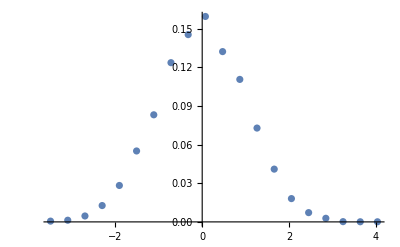

```mathematica
data={{-3.49168,0.0006},{-3.09553,0.0013},{-2.69937,0.0046},{-2.30322,0.0127},{-1.90707,0.0283},{-1.51091,0.0551},{-1.11476,0.0832},{-0.718608,0.1237},{-0.322455,0.1455},{0.0736986,0.1596},{0.469852,0.1323},{0.866005,0.1107},{1.26216,0.0729},{1.65831,0.041},{2.05446,0.0181},{2.45062,0.0072},{2.84677,0.0028},{3.24292,0.0002},{3.63908,0.0001},{4.03523,0.0001}};
ListPlot[data]
```

```mathematica
model=amplitude/(sigma Sqrt[2 Pi]) Exp[-(x-mean)^2/(2 sigma^2)];
fit=NonlinearModelFit[data,model,{{amplitude,1},{mean,0},{sigma,1}},x]
fit["ParameterTable"]
```

FittedModel[0.154961 ⅇ^(-0.477731 (0.00984386+x)^2)]

| Estimate | Standard Error | t-Statistic | P-Value
amplitude | 0.39738 | 0.00381191 | 104.247 | 2.67055×10^-25
mean | -0.00984386 | 0.0113317 | -0.868701 | 0.397109
sigma | 1.02304 | 0.011332 | 90.2791 | 3.06819×10^-24

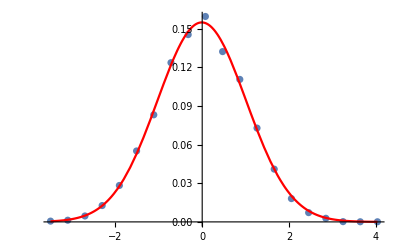

```mathematica
Show[ListPlot[data],Plot[fit[x],{x,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Red]]
```